```mathematica
Quit[]
```

## Load Model and Compute Diagrams

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
$FCVerbose=0;
Needs["FeynCalc`"]
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$FAVerbose=0;
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;

(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-SMQCD-NLO_FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
```

## g-g- t- t (self energy)

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →4, with {} →{-F[9],F[9],V[4],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3,p4}).
However the choice below produces nicer diagrams.

```mathematica
topsCT = CreateCTTopologies[1,2->2,ExcludeTopologies->{WFCorrectionCTs,TadpoleCTs,BoxCTs,TriangleCTs}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,WFCorrections}];
processGGT = { V[1],V[1]} -> {F[3],-F[3]};
allDiags = InsertFields[Join[topsCT,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1]}];
```

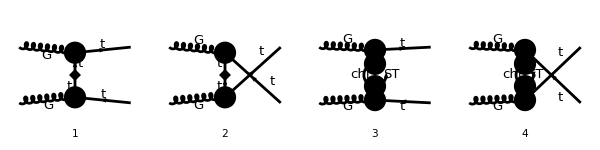

```mathematica
goodDiags=DiagramExtract[allDiags,{1,2,10,11}];
Paint[goodDiags,ColumnsXRows->{4,1},ImageSize->{ 600,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

## Compute Amplitude

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{-p4,-p3},LorentzIndexNames->{ν,μ},OutgoingMomenta->{p2,p1},LoopMomenta->{q},SUNIndexNames->{cc3,cc4,aa,bb},SUNFIndexNames->{a,b,c2,c1},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,FR$deltaZ[{G,G},{{}}]->deltaZG,FR$deltaZ[{t,t},{{}},"L"]->deltaZL,FR$deltaZ[{t,t},{{}},"R"]->deltaZR,FR$delta[{MT},{}]->deltaM,FR$delta[{aS},{}]->deltaaS};
ampB =FullSimplify[DiracSimplify[FCReplaceMomenta[SUNSimplify[DiracSimplify[ampA]],{p4-> -p1-p2-p3}]]];
```

```mathematica
CTsubs={deltaZG->0,deltaaS->0,deltaZL -> Pi^2yDM^2  MT^2  Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]],deltaZR-> Pi^2  yDM^2( MT^2 Re[DB1[MT^2,mChi^2,mST^2,BReduce->False]]+PaVe[1,{MT^2},{mChi^2,mST^2},PaVeAutoOrder->False,PaVeAutoReduce->False]),deltaM->-Pi^2/2 yDM^2 MT PaVe[1,{MT^2},{mChi^2,mST^2},PaVeAutoOrder->False,PaVeAutoReduce->False]};
ampB2=ampB/.CTsubs;
```

Evaluate Loop integrals:

```mathematica
ampC =FCCanonicalizeDummyIndices[( TID[ampB2,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True,PaVeAutoOrder->False]//Simplify),LorentzIndexNames-> {μ,ν}];
```

```mathematica
FCClearScalarProducts[];
SPD[p1,p2]=1/2(SPD[p3,p3]-SPD[p1,p1]-SPD[p2,p2]);
ampD=FullSimplify[DiracSimplify[ampC]];
ampEsimp2=Simplify[(ExpandScalarProduct[DiracSimplify[ampD]])];
```

## Check Divergences (note that the DB1 loop integral is finite)

```mathematica
lInts = Cases2[ampEsimp2,{A0,B0,C0,D0,B1,DB1,PaVe}];
lIntsUV=Table[lInt->PaXEvaluateUV[lInt,PaXImplicitPrefactor->1/(2 Pi)^4],{lInt,lInts}];
lIntsUV//MatrixForm
```

PaXEvaluate::convFail: Warning! Not all scalar loop integrals in the expression could be prepared to be processed with Package X. Following integrals will not be handled by Package X: {DB1(MT^2,mChi^2,mST^2,BReduce→False)}

(B_0(p1^2+2 (p1·p3)+p3^2,mChi^2,mST^2)→1/(16 π^4 ε_UV)
B_0(p2^2+2 (p2·p3)+p3^2,mChi^2,mST^2)→1/(16 π^4 ε_UV)
DB1(MT^2,mChi^2,mST^2,BReduce→False)→0
B_1(MT^2,mChi^2,mST^2)→-1/(32 π^4 ε_UV)
B_1(2 (p1·p3)+p1^2+p3^2,mST^2,mChi^2)→-1/(32 π^4 ε_UV)
B_1(2 (p2·p3)+p2^2+p3^2,mST^2,mChi^2)→-1/(32 π^4 ε_UV))

```mathematica
loopUV=FullSimplify[DiracSimplify[ampEsimp2/.lIntsUV,DiracSubstitute67->True]]
```

-(ⅈ gs^2 MT yDM^2 (((T^cc3 T^cc4)_c2c1 (-2 γ^ν.γ^μ (p1·p3)+γ^ν.(γ·p1).(γ·p3).γ^μ+γ^ν.(γ·p3).(γ·p1).γ^μ))/(((p1+p3)^2-MT^2)^2)+((T^cc4 T^cc3)_c2c1 (-2 γ^μ.γ^ν (p2·p3)+γ^μ.(γ·p2).(γ·p3).γ^ν+γ^μ.(γ·p3).(γ·p2).γ^ν))/(((p2+p3)^2-MT^2)^2)))/(32 π^2 ε_UV)

## Simplify Result

```mathematica
ampEsimp3a=Simplify[DiracSimplify[FeynAmpDenominatorExplicit[ampEsimp2]]];
```

### Order PaVe integrals

```mathematica
lInts = Cases2[ampEsimp3a,{A0,B0,C0,B1,D0,PaVe}];
orderedPaVes=Table[lInt->PaVeOrder[lInt,PaVeOrderList->{mST^2,mChi^2,mST^2,mST^2},Sum->True],{lInt,lInts}];
ampEsimp4=ampEsimp3a/.orderedPaVes;
lIntsOrdered = Cases2[ampEsimp4,{A0,B0,C0,D0,B1,PaVe}];
lIntsOrdered//MatrixForm
```

(D_0(p1sq,p2sq,p3sq,p4sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_0(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
C_1(p1sq,s,p2sq,mChi^2,mST^2,mST^2)
C_1(p2sq,s,p1sq,mChi^2,mST^2,mST^2)
D_1(p1sq,p2sq,p3sq,p4sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_1(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_2(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_2(p1sq,t,p4sq,s,p3sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_2(p1sq,u,p3sq,s,p4sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_2(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_00(p1sq,p2sq,p3sq,p4sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_00(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_11(p1sq,p2sq,p3sq,p4sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_11(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_12(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_12(p1sq,t,p4sq,s,p3sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_12(p1sq,u,p3sq,s,p4sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_12(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_22(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_22(p1sq,t,p4sq,s,p3sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_22(p1sq,u,p3sq,s,p4sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_22(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_23(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_23(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_001(p1sq,p2sq,p3sq,p4sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_001(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_002(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_002(p1sq,t,p4sq,s,p3sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_002(p1sq,u,p3sq,s,p4sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_002(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_111(p1sq,p2sq,p3sq,p4sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_111(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_112(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_112(p1sq,t,p4sq,s,p3sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_112(p1sq,u,p3sq,s,p4sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_112(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_122(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_122(p1sq,t,p4sq,s,p3sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_122(p1sq,u,p3sq,s,p4sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_122(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_123(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_123(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_222(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_222(p1sq,t,p4sq,s,p3sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_222(p1sq,u,p3sq,s,p4sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_222(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_223(p1sq,p2sq,p4sq,p3sq,s,t,mST^2,mChi^2,mST^2,mST^2)
D_223(p1sq,t,p4sq,s,p3sq,p2sq,mST^2,mChi^2,mST^2,mST^2)
D_223(p2sq,p1sq,p4sq,p3sq,s,u,mST^2,mChi^2,mST^2,mST^2)
D_223(p2sq,u,p4sq,s,p3sq,p1sq,mST^2,mChi^2,mST^2,mST^2))

### Make propagators explicit

```mathematica
ampEsimp5=FeynAmpDenominatorExplicit[DiracSimplify[ampEsimp4]];
```

## Extract Color and Lorentz (Tensor) Structure

First group terms by number of gamma matrices and momenta

```mathematica
spinorChains=DeleteDuplicates@Select[Cases[ampEsimp5,_Dot,Infinity],VectorQ[List@@#,MatchQ[#,_DiracGamma]&]&];
singleGamma=DeleteDuplicates@Cases[Select[ampEsimp5,Count[#,_DiracGamma,Infinity]==1&],_DiracGamma,All];
diracStructures=Sort[DeleteDuplicates@Join[singleGamma,spinorChains]]
momentumStructures=Sort[Join[{1},Cases2[ampEsimp5,Pair,All]]];
(* Remove appearances of pi^2, since they do not contribute to the tensor structure*)
momentumStructures=DeleteCases[momentumStructures,Pair[Momentum[a_,___],Momentum[a_,___]],All]
colorStructures = Sort[Join[Cases2[ampEsimp5,SUNTF],Cases2[ampEsimp5,SUNF]]]
```

{γ^μ.(γ̄)^6,γ^ν.(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6,(γ·p3).(γ̄)^6}

{1,g^μν,p1^μ,p2^μ,p3^μ,p1^ν,p2^ν,p3^ν}

{(T^cc3 T^cc4)_c2c1,(T^cc4 T^cc3)_c2c1}

### Split terms according to the tensor structure and color structure and factor out the vertex coupling

```mathematica
ampEsimp6=Collect[Expand[ampEsimp5],_PaVe,Simplify];
```

```mathematica
couplingTerms=DeleteDuplicates[(gs^Exponent[#,gs] yDM^Exponent[#,yDM])&/@List@@Expand[ampEsimp6]];
globalFactor = I Pi^2;structTerms=DeleteDuplicates[Simplify[Table[Times@@Flatten[Table[{d^{Exponent[term,d]}},{dList,{diracStructures,momentumStructures}},{d,dList}]],{term,List@@Expand[ampEsimp6]}]]];
coefficients=Join@@Join@@Table[{coupling*globalFactor,colorStructure,structure,Collect[Expand[Coefficient[Coefficient[Coefficient[Expand[ampEsimp6/globalFactor],coupling],colorStructure],structure]],{_C00,_B1,_PaVe},FullSimplify]},{structure,structTerms},{colorStructure,colorStructures},{coupling,couplingTerms}];
(* Select only non-zero coefficients *)
coefficients=Select[coefficients,#[[-1]]=!=0&];
```

Check that the coefficients really give the full result

```mathematica
ampTot =Sum[Times@@c,{c,coefficients}];
Simplify[ampTot-ampEsimp6]
```

0

## Check ALOHA conversion

```mathematica
Needs["alohaTranslator`"]
```

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g ] ] = [ p1=P(*,1),  p2=P(*,2), p3(μ)=P(*,3) ] (all momenta are incoming)
c2 = Top color = "2", c1 = Anti-Top color = "1", c3 = Gluon color = "3"
spins = [2, 2, 3], 
structure = ' P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)')
(The indices of the product of gamma matrices are always M(2,1), since the second (outgoing) top is contracted to the left and the first (incoming) to the right)

### Define relevant input for numbering the ALOHA indices:

```mathematica
gluon1Index=3;
gluon2Index=4;
topIndex=2;
antiTopIndex=1;
leftIndex=topIndex;
rightIndex=antiTopIndex;
momentumMap=<|p1->antiTopIndex,p2->topIndex,p3->gluon1Index,p4->gluon2Index|>;
lorentzMap=<|μ->gluon1Index,ν->gluon2Index|>;
colorMap=<|cc3->gluon1Index,cc4->gluon2Index,c2->topIndex,c1->antiTopIndex|>;
opts=Sequence@@{MomentumMap->momentumMap,LorentzMap->lorentzMap,ColorMap->colorMap,
LeftIndex->leftIndex,RightIndex->rightIndex};
```

Define additional translations which might be needed:

```mathematica
alohaDispatch[gs]:="G";
alohaDispatch[Pi]:="cmath.pi";
```

### Simplify the loop function notation so only the momenta appears in the expressions and convert it to collier notation

```mathematica
Needs["PaVeToCollierConverter`"]
convert2Collier=Table[lInt->PaVeToCollier[lInt,MassList->{mST^2,mChi^2,mST^2,mST^2}],{lInt,lIntsOrdered}];
lIntsOrdered/.convert2Collier//MatrixForm;
coefficientSimp=coefficients/.convert2Collier;
```

### Replace momenta squared by proper momentum products

```mathematica
FCClearScalarProducts[];
momRep={p1sq->Pair[Momentum[p1,D],Momentum[p1,D]],p2sq->Pair[Momentum[p2,D],Momentum[p2,D]],p3sq->Pair[Momentum[p3,D],Momentum[p3,D]],p4sq->Pair[Momentum[p4,D],Momentum[p4,D]],s->p1sq+p2sq+2Pair[Momentum[p1,D],Momentum[p2,D]],u->p1sq+p4sq+2Pair[Momentum[p1,D],Momentum[p4,D]],t->p1sq+p3sq+2Pair[Momentum[p1,D],Momentum[p3,D]]};
coefficientSimp2=coefficientSimp//.momRep;
```

### Convert to ALOHA splitting the color and tensor structure:

```mathematica
coefficientsALOHA=Table[Table[alohaTranslator[term,opts],{term,c}],{c,coefficientSimp2}];
```

```mathematica
coefficientSimp2[[1]]
coefficientsALOHA[[1]]
```

{ⅈ gs^2 π^2 yDM^2,(T^cc3 T^cc4)_c2c1,(γ·p2).(γ̄)^6 p3^μ p1^ν,-Dcoll(0,0,0,0,p1^2,p2^2,p3^2,p4^2,p1^2+2 (p1·p2)+p2^2,p1^2+2 (p1·p4)+p4^2)-2 Dcoll(0,0,1,0,p1^2,p1^2+2 (p1·p4)+p4^2,p3^2,p1^2+2 (p1·p2)+p2^2,p4^2,p2^2)-3 Dcoll(0,0,1,0,p2^2,p1^2,p4^2,p3^2,p1^2+2 (p1·p2)+p2^2,p1^2+2 (p1·p4)+p4^2)-6 Dcoll(0,0,1,1,p2^2,p1^2,p4^2,p3^2,p1^2+2 (p1·p2)+p2^2,p1^2+2 (p1·p4)+p4^2)-2 Dcoll(0,0,2,0,p2^2,p1^2,p4^2,p3^2,p1^2+2 (p1·p2)+p2^2,p1^2+2 (p1·p4)+p4^2)-4 Dcoll(0,0,2,1,p2^2,p1^2,p4^2,p3^2,p1^2+2 (p1·p2)+p2^2,p1^2+2 (p1·p4)+p4^2)-Dcoll(0,1,0,0,p1^2,p2^2,p3^2,p4^2,p1^2+2 (p1·p2)+p2^2,p1^2+2 (p1·p4)+p4^2)-2 Dcoll(0,1,1,0,p1^2,p1^2+2 (p1·p4)+p4^2,p3^2,p1^2+2 (p1·p2)+p2^2,p4^2,p2^2)-2 Dcoll(0,1,1,0,p2^2,p1^2,p4^2,p3^2,p1^2+2 (p1·p2)+p2^2,p1^2+2 (p1·p4)+p4^2)-4 Dcoll(0,1,1,1,p2^2,p1^2,p4^2,p3^2,p1^2+2 (p1·p2)+p2^2,p1^2+2 (p1·p4)+p4^2)}

{complex(0,1)*(G)**2*(cmath.pi)**2*(yDM)**2,T(3,2,-1)*T(4,-1,1),P(-2,2)*Gamma(-2,2,-1)*ProjP(-1,1)*P(3,3)*P(4,1),-1*Dcoll( 0, 0, 0, 0, P(-1,1)*P(-1,1), P(-2,2)*P(-2,2), P(-3,3)*P(-3,3), P(-4,4)*P(-4,4), P(-5,1)*P(-5,1) + 2*P(-6,1)*P(-6,2) + P(-7,2)*P(-7,2), P(-8,1)*P(-8,1) + 2*P(-9,1)*P(-9,4) + P(-10,4)*P(-10,4) ) + -2*Dcoll( 0, 0, 1, 0, P(-11,1)*P(-11,1), P(-12,1)*P(-12,1) + 2*P(-13,1)*P(-13,4) + P(-14,4)*P(-14,4), P(-15,3)*P(-15,3), P(-16,1)*P(-16,1) + 2*P(-17,1)*P(-17,2) + P(-18,2)*P(-18,2), P(-19,4)*P(-19,4), P(-20,2)*P(-20,2) ) + -3*Dcoll( 0, 0, 1, 0, P(-21,2)*P(-21,2), P(-22,1)*P(-22,1), P(-23,4)*P(-23,4), P(-24,3)*P(-24,3), P(-25,1)*P(-25,1) + 2*P(-26,1)*P(-26,2) + P(-27,2)*P(-27,2), P(-28,1)*P(-28,1) + 2*P(-29,1)*P(-29,4) + P(-30,4)*P(-30,4) ) + -6*Dcoll( 0, 0, 1, 1, P(-31,2)*P(-31,2), P(-32,1)*P(-32,1), P(-33,4)*P(-33,4), P(-34,3)*P(-34,3), P(-35,1)*P(-35,1) + 2*P(-36,1)*P(-36,2) + P(-37,2)*P(-37,2), P(-38,1)*P(-38,1) + 2*P(-39,1)*P(-39,4) + P(-40,4)*P(-40,4) ) + -2*Dcoll( 0, 0, 2, 0, P(-41,2)*P(-41,2), P(-42,1)*P(-42,1), P(-43,4)*P(-43,4), P(-44,3)*P(-44,3), P(-45,1)*P(-45,1) + 2*P(-46,1)*P(-46,2) + P(-47,2)*P(-47,2), P(-48,1)*P(-48,1) + 2*P(-49,1)*P(-49,4) + P(-50,4)*P(-50,4) ) + -4*Dcoll( 0, 0, 2, 1, P(-51,2)*P(-51,2), P(-52,1)*P(-52,1), P(-53,4)*P(-53,4), P(-54,3)*P(-54,3), P(-55,1)*P(-55,1) + 2*P(-56,1)*P(-56,2) + P(-57,2)*P(-57,2), P(-58,1)*P(-58,1) + 2*P(-59,1)*P(-59,4) + P(-60,4)*P(-60,4) ) + -1*Dcoll( 0, 1, 0, 0, P(-61,1)*P(-61,1), P(-62,2)*P(-62,2), P(-63,3)*P(-63,3), P(-64,4)*P(-64,4), P(-65,1)*P(-65,1) + 2*P(-66,1)*P(-66,2) + P(-67,2)*P(-67,2), P(-68,1)*P(-68,1) + 2*P(-69,1)*P(-69,4) + P(-70,4)*P(-70,4) ) + -2*Dcoll( 0, 1, 1, 0, P(-71,1)*P(-71,1), P(-72,1)*P(-72,1) + 2*P(-73,1)*P(-73,4) + P(-74,4)*P(-74,4), P(-75,3)*P(-75,3), P(-76,1)*P(-76,1) + 2*P(-77,1)*P(-77,2) + P(-78,2)*P(-78,2), P(-79,4)*P(-79,4), P(-80,2)*P(-80,2) ) + -2*Dcoll( 0, 1, 1, 0, P(-81,2)*P(-81,2), P(-82,1)*P(-82,1), P(-83,4)*P(-83,4), P(-84,3)*P(-84,3), P(-85,1)*P(-85,1) + 2*P(-86,1)*P(-86,2) + P(-87,2)*P(-87,2), P(-88,1)*P(-88,1) + 2*P(-89,1)*P(-89,4) + P(-90,4)*P(-90,4) ) + -4*Dcoll( 0, 1, 1, 1, P(-91,2)*P(-91,2), P(-92,1)*P(-92,1), P(-93,4)*P(-93,4), P(-94,3)*P(-94,3), P(-95,1)*P(-95,1) + 2*P(-96,1)*P(-96,2) + P(-97,2)*P(-97,2), P(-98,1)*P(-98,1) + 2*P(-99,1)*P(-99,4) + P(-100,4)*P(-100,4) )}

## Write Form Factors to UFO model

```mathematica
Needs["UFOFormFactorExport`"]
```

```mathematica
originalModel="../../UFO_models/SMS-stop_FormFactors-UFO_ttG/";
newModel="../../UFO_models/SMS-stop_FormFactors-UFO/";
fortranFolder ="../../auxFiles/Fortran"; (* also copy the required fortran functions to the new folder *)
If[Not[DirectoryQ[newModel]],CopyDirectory[originalModel,newModel]; CopyDirectory[fortranFolder,FileNameJoin[{newModel,"Fortran"}]]];
couplingOrders=<| yDM->"'NP'",gs->"'QCD'"|>;
spins = { 2, 2, 3, 3 };
particles = {"t__tilde__", "t", "g", "g"};
formFactorTag = "ff_FFVV";
header="----------- New entries for t-t-G-G (box) coupling --------";
alohaOptions=opts;
```

```mathematica
ExportUFOVertexFormFactors[coefficientSimp2,originalModel,newModel,CouplingOrders->couplingOrders,Spins->spins,Particles->particles,FormFactorTag->formFactorTag,AlohaOptions->opts,Header->header]
```

Writing to file: ../../UFO_models/SMS-stop_FormFactors-UFO/couplings.py

Writing to file: ../../UFO_models/SMS-stop_FormFactors-UFO/lorentz.py

Writing to file: ../../UFO_models/SMS-stop_FormFactors-UFO/vertices.py

V_125